```mathematica
(* =====================================================================*)(*Quantum metric g_xx,g_yy,g_xy of the critical band (band 3) of*)(*biased bilayer graphene,four-band model,valley K.*)(*Slider:interlayer bias V.The van Hove saddles (black dots) merge*)(*into the monkey saddle at V=Vc and reopen on the other side.*)(* =====================================================================*)

ClearAll["Global`*"];

(*----------1. Parameters and Hamiltonian---------------------------*)
v=0.658;g1=0.400;v3=0.1 v;            (*eV nm,eV,eV nm*)
Vc=g1 v3/v;                                  (*critical bias=0.040 eV*)
A=2 v^3/g1^2;B=v^5/(g1^3 v3);             (*monkey-saddle coefficients at Vc*)
ks=A/B;Es=A^4/B^3;                        (*k* =0.1216 nm^-1,E* =6.40 meV*)

(*basis (A1,B1,A2,B2);H=H0(V)+kx dHx+ky dHy*)
H0[V_]:={{V/2,0,0,0},{0,V/2,g1,0},{0,g1,-V/2,0},{0,0,0,-V/2}};
dHx={{0,v,0,v3},{v,0,0,0},{0,0,0,v},{v3,0,v,0}};
dHy={{0,-I v,0,I v3},{I v,0,0,0},{0,0,0,-I v},{-I v3,0,I v,0}};
Hk[kx_,ky_,V_]:=H0[V]+kx dHx+ky dHy;
```

```mathematica
eps3[kx_?NumericQ,ky_?NumericQ,V_?NumericQ]:=Sort[Re@Eigenvalues[N@Hk[kx,ky,V]]][[3]];

(*----------2. Metric of band 3 by the exact sum over states---------*)
(*g_ij=sum_{m!=3} Re[<3|dH_i|m><m|dH_j|3>]/(e3-em)^2*)
(*returns {gxx,gyy,gxy,e3}*)
metric[kx_?NumericQ,ky_?NumericQ,V_?NumericQ]:=Module[{es,vs,ord,e,u,vx,vy,gxx=0.,gyy=0.,gxy=0.,d},{es,vs}=Eigensystem[N@Hk[kx,ky,V]];
ord=Ordering[Re[es]];e=Re[es[[ord]]];u=Normalize/@vs[[ord]];
vx=Conjugate[u].dHx.Transpose[u];
vy=Conjugate[u].dHy.Transpose[u];
Do[If[m!=3,d=e[[3]]-e[[m]];
gxx+=Abs[vx[[3,m]]]^2/d^2;
gyy+=Abs[vy[[3,m]]]^2/d^2;
gxy+=Re[vx[[3,m]] vy[[m,3]]]/d^2],{m,4}];
{gxx,gyy,gxy,e[[3]]}];
```

```mathematica
(*check at k=0 against the closed form g=v3^2/V^2+v^2(g1^2+V^2)/g1^4*){metric[0.,0.,Vc][[1]],v3^2/Vc^2+v^2 (g1^2+Vc^2)/g1^4}    (*both 5.4391 nm^2*)

(*----------3. Critical points (van Hove saddles,minivalleys)-------*)
(*Scan the mirror rays phi=0 (descending) and phi=pi/3 (ascending).phi=0:radial maximum->saddle (V<Vc);radial minimum->minivalley phi=pi/3:radial minimum->saddle (V>Vc)*)
crit[V_]:=Module[{pg=Subdivide[0.0005,1.6 ks,1600],es,d,res={}},Do[es=eps3[# Cos[phi],# Sin[phi],V]&/@pg;d=Differences[es];
Do[If[d[[i]] d[[i+1]]<0,AppendTo[res,<|"phi"->phi,"p"->pg[[i+1]],"E"->es[[i+1]],"type"->If[d[[i]]>0,"max","min"]|>]],{i,Length[d]-1}],{phi,{0.,N[Pi/3]}}];
res];
rot3[{x_,y_}]:=Table[RotationMatrix[2 Pi j/3].{x,y},{j,0,2}];
saddlesOf[cr_]:=Select[cr,(#phi==0.&&#type=="max")||(#phi>0&&#type=="min")&];
valleysOf[cr_]:=Select[cr,#phi==0.&&#type=="min"&];
ptsOf[list_]:=Flatten[rot3[#p {Cos[#phi],Sin[#phi]}/ks]&/@list,1];   (*in units of k**)
```

{5.43911,5.43911}

```mathematica
(*----------4. Precompute maps for a set of biases-------------------*)qmax=1.3;nq=81;qs=Subdivide[-qmax,qmax,nq-1];
rList=Range[0.6,1.4,0.05];                       (*V/Vc*)
data=Table[Table[metric[qx ks,qy ks,r Vc],{qy,qs},{qx,qs}],(*rows=qy,columns=qx*){r,rList}];                                     (*about 110k diagonalisations;replace the outer Table by ParallelTable to use all cores*)
crits=Table[crit[r Vc],{r,rList}];

(*fixed colour scales for all biases,so the frames can be compared*)
gmax=Quantile[Flatten[data[[All,All,All,1;;2]]],0.98];
gxyMax=Quantile[Abs@Flatten[data[[All,All,All,3]]],0.98];

(*----------5. Brown-orange palettes---------------------------------*)
seqCol=Blend[{RGBColor[0.99,0.94,0.84],RGBColor[0.97,0.72,0.30],RGBColor[0.86,0.47,0.13],RGBColor[0.56,0.28,0.08],RGBColor[0.24,0.11,0.03]},#]&;
divCol=Blend[{{-1,RGBColor[0.30,0.15,0.04]},{-0.45,RGBColor[0.66,0.40,0.18]},{0,RGBColor[1,0.97,0.92]},{0.45,RGBColor[0.98,0.71,0.32]},{1,RGBColor[0.91,0.43,0.05]}},#]&;

(*----------6. One panel----------------------------------------------*)
panel[i_,comp_]:=Module[{r=rList[[i]],M,E3,cr,sad,val,Evhs,base,lines,cf,lims,lab},M=data[[i,All,All,comp]];
E3=(data[[i,All,All,4]]-r Vc/2) 1000;(*meV,from the k=0 energy*)cr=crits[[i]];sad=saddlesOf[cr];val=valleysOf[cr];
Evhs=If[sad==={},0.,1000 (First[sad]["E"]-r Vc/2)];(*van Hove energy*){cf,lims}=If[comp==3,{divCol[Clip[#/gxyMax,{-1,1}]]&,{-gxyMax,gxyMax}},{seqCol[Clip[#/gmax,{0,1}]]&,{0,gmax}}];
lab={"\!\(\*SubscriptBox[\(g\), \(xx\)]\)","\!\(\*SubscriptBox[\(g\), \(yy\)]\)","\!\(\*SubscriptBox[\(g\), \(xy\)]\)"}[[comp]];
base=ListContourPlot[M,DataRange->{{-qmax,qmax},{-qmax,qmax}},Contours->Subdivide[lims[[1]],lims[[2]],16],ColorFunction->cf,ColorFunctionScaling->False,ContourStyle->Directive[GrayLevel[0.3],Opacity[0.35],AbsoluteThickness[0.5]],PlotRange->{All,All,All},InterpolationOrder->2,PlotLegends->BarLegend[{cf,lims},LegendLabel->lab<>" (nm.b2)"]];
lines=ListContourPlot[E3,DataRange->{{-qmax,qmax},{-qmax,qmax}},Contours->{Evhs},ContourShading->None,ContourStyle->Directive[Black,AbsoluteThickness[1.8]],InterpolationOrder->2];
Show[base,lines,Epilog->{{Black,PointSize[0.035],Point[ptsOf[sad]]},(*van Hove saddles*){EdgeForm[Black],White,Disk[#,0.04]&/@ptsOf[val]},(*minivalley minima*){If[Abs[r-1]<10^-6,Red,GrayLevel[0.2]],PointSize[0.03],Point[{0,0}]}},(*k=0;red at Vc*)FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\)/k*","\!\(\*SubscriptBox[\(k\), \(y\)]\)/k*"},PlotLabel->lab,ImageSize->300,AspectRatio->1]];
```

```mathematica
Manipulate[Module[{r=rList[[i]],sad=saddlesOf[crits[[i]]]},Column[{Style[Row[{"V/Vc = ",NumberForm[r,{3,2}],"     V = ",NumberForm[1000 r Vc,{4,1}]," meV     ",If[sad==={},If[Abs[r-1]<10^-6,"monkey saddle at k = 0 (VHS closed into one point)","no saddle on the mirror rays"],Row[{"van Hove energy  E_s - V/2 = ",NumberForm[1000 (First[sad]["E"]-r Vc/2),{4,4}]," meV,  |k_s|/k* = ",NumberForm[First[sad]["p"]/ks,{3,3}]}]]}],13],Row[{panel[i,1],panel[i,2],panel[i,3]},Spacer[8]],Style["black dots: van Hove saddles;  white disks: minivalley minima;  black line: van Hove contour;  red dot: monkey saddle (V = Vc)",10,Gray]}]],{{i,Position[rList,_?(Abs[#-1]<10^-6&)][[1,1]],"bias index"},1,Length[rList],1,Appearance->"Labeled"},TrackedSymbols:>{i},SaveDefinitions->True]
```

```mathematica
(* =====================================================================*)(*Generalized electric susceptibility (GES) of biased bilayer graphene*)(*Kitamura,Daido,Yanase,PRL 132,036001 (2024),Eqs.(1)-(2):*)(**)(*chi_e^{mu nu}=lim_{q->0} d_{q_mu} d_{q_nu} chi^0(q)*)(*               =chi_geom+chi_mass*)(*chi_geom=2 Sum_n Int d^2k/(2pi)^2[f'(e_n)/2 g_n+f(e_n) X_n]*)(*chi_mass=-2 Sum_n Int d^2k/(2pi)^2 f''(e_n)/12[m_n^{-1}]*)(**)(*g_n^{mu nu}=Sum_{m!=n} (A^mu_nm A^nu_mn+c.c.) (=2 x standard)*)(*X_n^{mu nu}=Sum_{m!=n} (A^mu_nm A^nu_mn+c.c.)/(e_m-e_n)*)(*[m_n^{-1}]^{mu nu}=d_mu d_nu e_n,A^mu_nm=i<d_mu u_n|u_m>*)(**)(*C3 symmetry=>xx=yy,xy=0;we use (xx+yy)/2.*)(*chi_e<0=>q=0 is a maximum of chi^0(q) (ferromagnetic*)(*fluctuation favoured);chi_e>0=>it is not.*)(*Results are per spin and per valley (the two valleys are equal by*)(*time reversal);units:chi_e in eV^-1,chi^0(0) in eV^-1 nm^-2.*)(* =====================================================================*)
```

```mathematica
(*----------1. Model (valley K,basis A1,B1,A2,B2)--------------------*)v=0.658;g1=0.400;v3=0.1 v;                 (*eV nm,eV,eV nm*)
Vc=g1 v3/v;                                       (*0.040 eV*)
A=2 v^3/g1^2;B=v^5/(g1^3 v3);ks=A/B;Es=A^4/B^3;   (*k* =0.1216 nm^-1,E* =6.40 meV*)
H0[V_]:={{V/2,0,0,0},{0,V/2,g1,0},{0,g1,-V/2,0},{0,0,0,-V/2}};
dHx={{0,v,0,v3},{v,0,0,0},{0,0,0,v},{v3,0,v,0}};
dHy={{0,-I v,0,I v3},{I v,0,0,0},{0,0,0,-I v},{-I v3,0,I v,0}};
eps3[kx_?NumericQ,ky_?NumericQ,V_?NumericQ]:=Sort[Re@Eigenvalues[N[H0[V]+kx dHx+ky dHy]]][[3]];

(*----------2. Band quantities at one k point--------------------------*)
(*For H linear in k:A^mu_nm=i v^mu_nm/(e_m-e_n),v^mu= <n|dH_mu|m>.Returns,for n=1..4 (ascending),the (xx+yy)/2 averages:e_n,g_n=Sum_m (|vx|^2+|vy|^2)/(e_n-e_m)^2,X_n=Sum_m (|vx|^2+|vy|^2)/(e_n-e_m)^2/(e_m-e_n),M_n=(d_xx+d_yy) e_n/2=Sum_m (|vx|^2+|vy|^2)/(e_n-e_m)*)
kData[kx_,ky_,V_]:=Module[{es,vs,ord,e,u,vx,vy,VV,DD},{es,vs}=Eigensystem[N[H0[V]+kx dHx+ky dHy]];
ord=Ordering[Re[es]];e=Re[es[[ord]]];u=Normalize/@vs[[ord]];
vx=Conjugate[u].dHx.Transpose[u];vy=Conjugate[u].dHy.Transpose[u];
VV=Abs[vx]^2+Abs[vy]^2;
DD=Outer[Subtract,e,e]+10.^15 IdentityMatrix[4];(*removes the m=n terms*){e,Total[VV/DD^2,{2}],Total[-VV/DD^3,{2}],Total[VV/DD,{2}]}];
```

```mathematica
(*----------3. Integration grids (Gauss-Legendre in|k|,uniform angle)-*)gaussRule=Most@NIntegrate`GaussRuleData[64,MachinePrecision];   (*nodes,weights on[0,1]*)
radial[edges_]:={Flatten@Table[edges[[i]]+(edges[[i+1]]-edges[[i]]) gaussRule[[1]],{i,Length[edges]-1}],Flatten@Table[(edges[[i+1]]-edges[[i]]) gaussRule[[2]],{i,Length[edges]-1}]};
polar[{p_,wp_},nphi_]:=Module[{ph=(Range[nphi]-0.5) 2. Pi/nphi},{Flatten@Outer[Times,p,Cos[ph]],Flatten@Outer[Times,p,Sin[ph]],Flatten@Outer[Times,wp p,ConstantArray[2. Pi/nphi,nphi]]/(4 Pi^2)}];   (*weights include d^2k/(2pi)^2*)
gridInner[kin_,np_,nphi_]:=polar[radial[Subdivide[0.,kin,np/64]],nphi];          (*np:multiple of 64*)
gridOuter[kin_,kmax_,nphi_,nseg_]:=polar[radial[Join[{kin},Exp@Subdivide[Log[1.05 kin],Log[kmax],nseg-1]]],nphi];

bandData[grid_,V_]:=Module[{res=MapThread[kData[#1,#2,V]&,Most[grid]]},{res[[All,1]],res[[All,2]],res[[All,3]],res[[All,4]],Last[grid]}];
```

```mathematica
(*----------4. GES and uniform susceptibility for given (mu,T)--------*)GES[dat_,mu_,T_]:=Module[{e,g,X,M,w,f,fp,fpp},{e,g,X,M,w}=dat;
f=LogisticSigmoid[-(e-mu)/T];fp=-f (1-f)/T;fpp=f (1-f) (1-2 f)/T^2;
<|"geomFS"->2 w.Total[fp g/2,{2}],(*quantum-metric (Fermi-surface) part, <=0*)"geomSea"->2 w.Total[f X,{2}],(*positional-shift (Fermi-sea) part, >=0*)"mass"->-2 w.Total[fpp M/12,{2}],(*effective-mass term*)"chi0"->w.Total[-fp,{2}]|>];       (*chi^0(q=0)=thermal DOS*)

(* |k| >kin:no Fermi surface;bands 1,2 filled and 3,4 empty,so only the positional-shift term survives.It does not depend on mu or T.Computed to kmax=20 and 80 nm^-1 and extrapolated linearly in 1/kmax.*)
seaOuter[V_,kin_]:=Module[{s},s[km_]:=Module[{d=bandData[gridOuter[kin,km,48,16],V]},2 d[[5]].(d[[3]].{1.,1.,0.,0.})];
With[{s20=s[20.],s80=s[80.]},(80 s80-20 s20)/60]];
```

```mathematica
(*----------5. Precompute the three biases-----------------------------*)
kin=0.36;nRad=768;nAng=288;            (* ~2.2e5 k points per bias*)
rList={0.8,1.0,1.2};                         (*V/Vc*)
AbsoluteTiming[dataV=Table[bandData[gridInner[kin,nRad,nAng],r Vc],{r,rList}];
outV=Table[seaOuter[r Vc,kin],{r,rList}];]
(*about 1e6 diagonalisations in total;to use all cores,replace MapThread in bandData by ParallelMap[kData[#[[1]],#[[2]],V]&,Transpose[Most[grid]]] after DistributeDefinitions[kData,H0,dHx,dHy,v,v3,g1]*)

chiE[i_,mu_,T_]:=Module[{a=GES[dataV[[i]],mu,T]},<|"geom"->a["geomFS"]+a["geomSea"]+outV[[i]],"metric"->a["geomFS"],"shift"->a["geomSea"]+outV[[i]],"mass"->a["mass"],"total"->a["geomFS"]+a["geomSea"]+outV[[i]]+a["mass"],"chi0"->a["chi0"]|>];

(*check against an independent Python implementation,mu=V/2,T=0.1 meV:V/Vc=0.8:chi_mass=20.53,chi_geom=-16.91,total=3.63,chi0=0.5727 V/Vc=1.0:chi_mass=25.82,chi_geom=-14.24,total=11.57,chi0=0.6418 V/Vc=1.2:chi_mass=20.17,chi_geom=-12.64,total=7.53,chi0=0.7000 (agreement to~1e-3 expected;the outer grid here is coarser)*)
Table[{rList[[i]],KeyTake[chiE[i,rList[[i]] Vc/2,1.*^-4],{"mass","geom","total","chi0"}]},{i,3}]//TableForm
```

{102.683,Null}

0.8 | <|mass→20.5342,geom→-16.9055,total→3.6287,chi0→0.572719|>
1. | <|mass→25.8177,geom→-14.2437,total→11.574,chi0→0.641807|>
1.2 | <|mass→20.169,geom→-12.6361,total→7.53288,chi0→0.700034|>

```mathematica
(*----------6. van Hove energies (saddle points on the mirror rays)----*)crit[V_]:=Module[{pg=Subdivide[0.0005,1.6 ks,1600],es,d,res={}},Do[es=eps3[# Cos[phi],# Sin[phi],V]&/@pg;d=Differences[es];
Do[If[d[[j]] d[[j+1]]<0,AppendTo[res,{phi,pg[[j+1]],es[[j+1]],If[d[[j]]>0,"max","min"]}]],{j,Length[d]-1}],{phi,{0.,N[Pi/3]}}];res];
vhsE[V_]:=Module[{c=crit[V],s},s=Select[c,(#[[1]]==0.&&#[[4]]=="max")||(#[[1]]>0&&#[[4]]=="min")&];
If[s==={},V/2,s[[1,3]]]];                                    (*at Vc:monkey saddle at k=0*)
edgeE[V_]:=Module[{c=Select[crit[V],#[[1]]==0.&&#[[4]]=="min"&]},If[c==={},Missing[],c[[1,3]]]];
Evhs=vhsE[# Vc]&/@rList;Eedge=edgeE[# Vc]&/@rList;
Table[{rList[[i]],"E_vhs - V/2 [meV]"->1000 (Evhs[[i]]-rList[[i]] Vc/2),"minivalley edge - V/2 [meV]"->1000 (Eedge[[i]]-rList[[i]] Vc/2)},{i,3}]//TableForm
```

0.8 | E_vhs - V/2 [meV]→0.000987787 | minivalley edge - V/2 [meV]→-0.461722
1. | E_vhs - V/2 [meV]→0. | minivalley edge - V/2 [meV]→-0.656676
1.2 | E_vhs - V/2 [meV]→-0.00092167 | minivalley edge - V/2 [meV]→-0.893584

```mathematica
(*----------7. Colours-------------------------------------------------*)cBrown=RGBColor[0.50,0.26,0.08];cOrange=RGBColor[0.93,0.52,0.12];
cBlack=GrayLevel[0.1];cTan=RGBColor[0.80,0.62,0.40];
```

```mathematica
(*----------8. Plot 1:chi_geom and chi_mass versus mu at low T,q=0--*)Tlow=1.*^-4;                                   (*0.1 meV;50 ueV is fine on this grid as well*)
dmuList=Subdivide[-1.2,3.0,84];              (*mu-V/2 in meV*)
scanMu=Table[With[{c=chiE[i,rList[[i]] Vc/2+0.001 dm,Tlow]},{dm,c["geom"],c["mass"],c["total"],c["metric"],c["shift"]}],{i,3},{dm,dmuList}];
GraphicsRow[Table[ListLinePlot[{scanMu[[i,All,{1,2}]],scanMu[[i,All,{1,3}]],scanMu[[i,All,{1,4}]]},PlotStyle->{Directive[cOrange,AbsoluteThickness[2]],Directive[cBrown,AbsoluteThickness[2],Dashed],Directive[cBlack,AbsoluteThickness[2.5]]},PlotLegends->If[i==3,{"\!\(\*SubscriptBox[\(χ\), \(geom\)]\)","\!\(\*SubscriptBox[\(χ\), \(mass\)]\)","\!\(\*SubscriptBox[\(χ\), \(e\)]\) total"},None],GridLines->{{1000 (Evhs[[i]]-rList[[i]] Vc/2),If[MissingQ[Eedge[[i]]],Nothing,1000 (Eedge[[i]]-rList[[i]] Vc/2)]},{0}},GridLinesStyle->Directive[Gray,Dashed],PlotRange->{All,{-60,120}},Frame->True,FrameLabel->{"μ - V/2 (meV)","GES  \!\(\*SuperscriptBox[\(χ\), \(0:xx\)]\) (\!\(\*SuperscriptBox[\(eV\), \(-1\)]\))"},PlotLabel->Row[{"V = ",rList[[i]]," \!\(\*SubscriptBox[\(V\), \(c\)]\),  T = ",1000 Tlow," meV"}],ImageSize->330],{i,3}],ImageSize->1080]
(*dashed vertical lines:van Hove energy and minivalley band edge*)

(*optional:split of chi_geom into quantum-metric and positional-shift parts*)
GraphicsRow[Table[ListLinePlot[{scanMu[[i,All,{1,5}]],scanMu[[i,All,{1,6}]],scanMu[[i,All,{1,2}]]},PlotStyle->{cTan,cBrown,Directive[cOrange,AbsoluteThickness[2]]},PlotLegends->If[i==3,{"quantum metric","positional shift","\!\(\*SubscriptBox[\(χ\), \(geom\)]\)"},None],Frame->True,FrameLabel->{"μ - V/2 (meV)","\!\(\*SuperscriptBox[\(eV\), \(-1\)]\)"},PlotLabel->Row[{"V = ",rList[[i]]," \!\(\*SubscriptBox[\(V\), \(c\)]\)"}],ImageSize->330],{i,3}],ImageSize->1080]
```

-Graphics-

-Graphics-

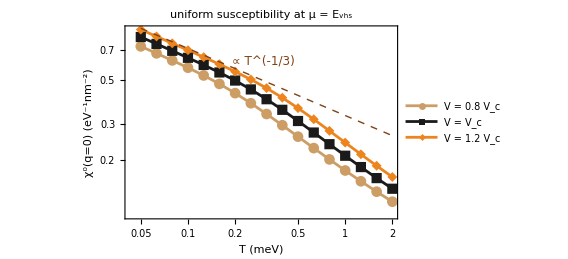

-Graphics-

```mathematica
(*----------9. Plot 2:temperature dependence at the van Hove energy----*)TList=10.^Subdivide[Log10[5.*^-5],Log10[2.*^-3],16];        (*0.05-2 meV*)
scanT=Table[With[{c=chiE[i,Evhs[[i]],T]},{1000 T,c["geom"],c["mass"],c["total"],c["chi0"]}],{i,3},{T,TList}];

(*(a) uniform spin susceptibility chi^0(q=0)=thermal DOS*)
ListLogLogPlot[Table[scanT[[i,All,{1,5}]],{i,3}],Joined->True,PlotMarkers->Automatic,PlotStyle->{cTan,cBlack,cOrange},PlotLegends->{"V = 0.8 \!\(\*SubscriptBox[\(V\), \(c\)]\)","V = \!\(\*SubscriptBox[\(V\), \(c\)]\)","V = 1.2 \!\(\*SubscriptBox[\(V\), \(c\)]\)"},Epilog->{Dashed,cBrown,Line[{Log[{0.05,0.9}],Log[{2.0,0.9 (2.0/0.05)^(-1/3)}]}],Text[Style["∝ \!\(\*SuperscriptBox[\(T\), \(-1/3\)]\)",12,cBrown],Log[{0.3,0.62}]]},Frame->True,FrameLabel->{"T (meV)","\!\(\*SuperscriptBox[\(χ\), \(0\)]\)(q=0) (\!\(\*SuperscriptBox[\(eV\), \(-1\)]\)\!\(\*SuperscriptBox[\(nm\), \(-2\)]\))"},PlotLabel->"uniform susceptibility at μ = \!\(\*SubscriptBox[\(E\), \(vhs\)]\)",ImageSize->420]

(*(b) GES components versus T at mu=E_vhs*)
GraphicsRow[Table[ListLogLinearPlot[{scanT[[i,All,{1,2}]],scanT[[i,All,{1,3}]],scanT[[i,All,{1,4}]]},Joined->True,PlotMarkers->{Automatic,7},PlotStyle->{Directive[cOrange,AbsoluteThickness[2]],Directive[cBrown,AbsoluteThickness[2],Dashed],Directive[cBlack,AbsoluteThickness[2.5]]},PlotLegends->If[i==3,{"\!\(\*SubscriptBox[\(χ\), \(geom\)]\)","\!\(\*SubscriptBox[\(χ\), \(mass\)]\)","\!\(\*SubscriptBox[\(χ\), \(e\)]\) total"},None],GridLines->{None,{0}},Frame->True,FrameLabel->{"T (meV)","GES (\!\(\*SuperscriptBox[\(eV\), \(-1\)]\))"},PlotLabel->Row[{"V = ",rList[[i]]," \!\(\*SubscriptBox[\(V\), \(c\)]\),  μ = \!\(\*SubscriptBox[\(E\), \(vhs\)]\)"}],ImageSize->330],{i,3}],ImageSize->1080]
```